```mathematica
ClearAll["Global`*"]
```

```mathematica
SetAttributes[saveSet,HoldAll];
saveSet[form:Set[var_,_]]:=(lastSet=ToString@Unevaluated@var;form);
saveSet[form:___]:=(lastSet=.;form)
$Pre=saveSet;
$Post=(If[ValueQ@lastSet,Row[{lastSet," = ",#}],#])&;
```

0.782

-1.804

9.

9.

9.

1.5

1.5

1.5

1.×10^52

1.×10^52

1.×10^52

2.6079

2.6079

2.6079

0.808255

8.56244

93.8998

10.4333

2.68566

2.68566

2.68566

101.823

101.823

101.823

11.3137

11.3137

12.4291

12.4291

31.1372

31.1372

31.1372

0.61608

0.637466

0.61244

9.

9.

101.823

101.823

11.3137

11.3137

12.4291

12.4291

0.61244

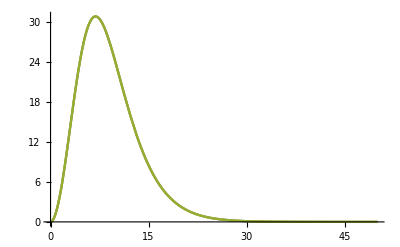

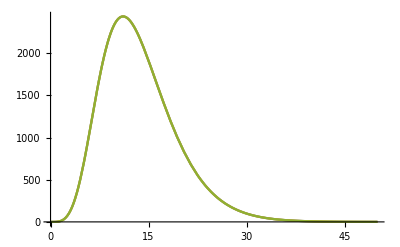

```mathematica
(* ℏc in MeV cm, c in cm/s, neutron-proton mass difference in MeV, neutrinosphere radius in km *)
ℏc = 1.97326979*^-11;
c = 2.99792458*^10;
erginMeV = 624151;
Δ=1.293;
me =0.511;
Qe = Δ-me
Qb = -Δ-me
Rnu = 19; (* For now, assume a single neutrinosphere for all flavors *)

(* Fermi-Dirac integrals *)
F[k_,η_] := NIntegrate[x^k/(Exp[x-η]+1),{x,0,∞}];

(*(* Eav = ,⟨E⟩; values taken from Bollig 1D at t ~ 2.0s. ηe and ηb adjusted to get approximate values of ,,⟨E^2⟩ as per Bollig *)
Le = 7.69*^51
Lb = 7.37*^51
Lx =9.4*^51
(*Eave = 9 (* test for many body nucleo calculation *) *)
Eave=11.43
Eavb=14.73
Eavx=14.41
(* ηe = 1.5 (* test for many body nucleo calculation *) *)
ηe=1.2
ηb=1.3 
ηx=0.4*)

(* Set nue and nuebar parameters equal to nux, as a test *)
 (* Le = Lx
Lb = Lx
Eave = Eavx
Eavb = Eavx
ηe = ηx
ηb = ηx *)


(* Bollig-1D 2s Lnu x nuebar fudge factor *)
(* Le = 7.69*^51
Lb =7.37*^51/1.1
Lx =9.4*^51 *)


(*(* Hudepohl params *)
Eave = 9.7
Eavb = 11.7
Eavx = 11.0
ηe = 2.1
ηb = 1.5
ηx = 0.4
(* Hudepohl Lnu x nuebar fudge factor *)
Le = 7.0*^51
Lb = Le/1.22
Lx = Le *)

(* Xilu calc params *)
Eave = 9.0
Eavb = 9.0
Eavx = 9.0
ηe = 1.5
ηb = 1.5
ηx = 1.5
(* Hudepohl Lnu x nuebar fudge factor *)
Le = 1.0*^52
Lb = 1.0*^52
Lx = 1.0*^52

(* Calculate Fermi-Dirac spectral temperatures from ⟨E⟩ and η *) 
Te =Eave/(F[3,ηe]/F[2,ηe])
Tb =Eavb/(F[3,ηb]/F[2,ηb])
Tx =Eavx/(F[3,ηx]/F[2,ηx])

(* Define "effective" electron anti-neutrino degeneracy parameter, accounting for nuebar capture cross-section being zero for E < |Q| *)
(* Also define corresponding energy averages, which will be used for calculating nuebar capture rates *)

ηbp = ηb+Qb/Tb
Eavbp = (F[3,ηbp]/F[2,ηbp])Tb
E2avbp = (F[4,ηbp]/F[3,ηbp])(F[2,ηbp]/F[3,ηbp])Eavbp^2
ϵbp = E2avbp/Eavb

(* Calculate normalization constants for the distributions, normalized to luminosities *)
Ne = (2π Le)/(Rnu^2 Te^4 F[3,ηe])erginMeV × (ℏc/1*^5)^2×ℏc/c
Nb = (2π Lb)/(Rnu^2 Tb^4 F[3,ηb])erginMeV × (ℏc/1*^5)^2×ℏc/c
Nx = (2π Lx)/(Rnu^2 Tx^4 F[3,ηx])erginMeV × (ℏc/1*^5)^2×ℏc/c

(* E2av = ⟨E^2⟩ *)
E2ave = (F[4,ηe]/F[3,ηe])(F[2,ηe]/F[3,ηe])Eave^2
E2avb = (F[4,ηb]/F[3,ηb])(F[2,ηb]/F[3,ηb])Eavb^2
E2avx = (F[4,ηx]/F[3,ηx])(F[2,ηx]/F[3,ηx])Eavx^2

(* ϵ and ε are defined as per Qian and Woosley (1996) *) 
(* ϵ = ⟨E^2⟩/⟨E⟩ = (Subscript[F, 4][η]/Subscript[F, 3][η])T = (Subscript[F, 4][η]/Subscript[F, 3][η])(Subscript[F, 2][η]/Subscript[F, 3][η])⟨E⟩  *)
(* ε = (⟨E^3⟩/⟨E⟩)^(1/2) = (Subscript[F, 5][η]/Subscript[F, 3][η])^(1/2)T = (Subscript[F, 5][η]/Subscript[F, 3][η])^(1/2) (Subscript[F, 2][η]/Subscript[F, 3][η])⟨E⟩ *) 
ϵe =Eave(F[4,ηe]/F[3,ηe])(F[2,ηe]/F[3,ηe])
ϵb =Eavb(F[4,ηb]/F[3,ηb])(F[2,ηb]/F[3,ηb])

εe=Eave*(F[5,ηe]/F[3,ηe])^(1/2)(F[2,ηe]/F[3,ηe])
εb=Eavb*(F[5,ηb]/F[3,ηb])^(1/2)(F[2,ηb]/F[3,ηb])

(* Calculate neutrinosphere radii assuming Blackbody emission; σs are the Stefan-Boltzmann constants *)
σe = 7/8 1/2 π^2/60 NIntegrate[x^3/(Exp[x-ηe]+1),{x,0,∞}]/NIntegrate[x^3/(Exp[x]+1),{x,0,∞}];
σb = 7/8 1/2 π^2/60 NIntegrate[x^3/(Exp[x-ηb]+1),{x,0,∞}]/NIntegrate[x^3/(Exp[x]+1),{x,0,∞}];
σx = 7/8 1/2 π^2/60 NIntegrate[x^3/(Exp[x-ηx]+1),{x,0,∞}]/NIntegrate[x^3/(Exp[x]+1),{x,0,∞}];
Rnue = Sqrt[Le*erginMeV*ℏc/c/(4π σe Te^4)]*ℏc/1*^5
Rnub = Sqrt[Lb*erginMeV*ℏc/c/(4π σb Tb^4)]*ℏc/1*^5
Rnux = Sqrt[Lx*erginMeV*ℏc/c/(4π σx Tx^4)]*ℏc/1*^5

(* Calculate Ye using Tian, Patwardhan, Fuller (2017) *)
YeTian =(1+Lb/Le(ϵb+2Qb+Qb^2/Eavb)/(ϵe+2Qe+Qe^2/Eave))^-1 
(* Corrected expression, accounting for nuebar capture cross section being zero at E < |Q| *)
Yecorr =(1+Lb/Le(ϵbp+2Qb Eavbp/Eavb+Qb^2/Eavb)/(ϵe+2Qe+Qe^2/Eave))^-1
(* Calculate Ye, using Qian and Woosley (1996), Eq. 77 *)
YeQian=(1+Lb/Le(ϵb-2Δ+Δ^2/Eavb)/(ϵe+2Δ+Δ^2/Eave))^-1

(* Now consider mixing with ν_(x .)Assume complete mixing so that Subscript[f, νe] -> (Subscript[f, νe] + 2 Subscript[f, νx])/3 *)
Eavemix = (Ne Te^4 F[3,ηe]+2Nx Tx^4 F[3,ηx])/(Ne Te^3 F[2,ηe]+2Nx Tx^3 F[2,ηx])
Eavbmix = (Nb Tb^4 F[3,ηb]+2Nx Tx^4 F[3,ηx])/(Nb Tb^3 F[2,ηb]+2Nx Tx^3 F[2,ηx])

(* E2av = ⟨E^2⟩ *)
E2avemix = (Ne Te^5 F[4,ηe]+2Nx Tx^5 F[4,ηx])/(Ne Te^3 F[2,ηe]+2Nx Tx^3 F[2,ηx])
E2avbmix =(Nb Tb^5 F[4,ηb]+2Nx Tx^5 F[4,ηx])/(Nb Tb^3 F[2,ηb]+2Nx Tx^3 F[2,ηx])

(* ϵ and ε are defined as per Qian and Woosley (1996) *) 
(* ϵ = ⟨E^2⟩/⟨E⟩ = (Subscript[F, 4][η]/Subscript[F, 3][η])T = (Subscript[F, 4][η]/Subscript[F, 3][η])(Subscript[F, 2][η]/Subscript[F, 3][η])⟨E⟩ *)
ϵemix =(Ne Te^5 F[4,ηe]+2Nx Tx^5 F[4,ηx])/(Ne Te^4 F[3,ηe]+2Nx Tx^4 F[3,ηx])
ϵbmix =(Nb Tb^5 F[4,ηb]+2Nx Tx^5 F[4,ηx])/(Nb Tb^4 F[3,ηb]+2Nx Tx^4 F[3,ηx])

(* ε = (⟨E^3⟩/⟨E⟩)^(1/2) = (Subscript[F, 5][η]/Subscript[F, 3][η])^(1/2)T = (Subscript[F, 5][η]/Subscript[F, 3][η])^(1/2) (Subscript[F, 2][η]/Subscript[F, 3][η])⟨E⟩ *) 
εemix=((Ne Te^6 F[5,ηe]+2Nx Tx^6 F[5,ηx])/(Ne Te^4 F[3,ηe]+2Nx Tx^4 F[3,ηx]))^(1/2)
εbmix=((Nb Tb^6 F[5,ηb]+2Nx Tx^6 F[5,ηx])/(Nb Tb^4 F[3,ηb]+2Nx Tx^4 F[3,ηx]))^(1/2)
Lemix = (Le +2 Lx)/3;
Lbmix = (Lb +2 Lx)/3;
Lemix/Lbmix;
Yemix=(1+Lbmix/Lemix(ϵbmix-2Δ+Δ^2/Eavbmix)/(ϵemix+2Δ+Δ^2/Eavemix))^-1
fe[x_] :=Ne x^2/(Exp[x/Te-ηe]+1);
fx[x_] :=Nx x^2/(Exp[x/Tx-ηx]+1);
fmix[x_] := 1/3 fe[x] + 2/3 fx[x];
Plot[{fe[x],fx[x],fmix[x]},{x,0,50},PlotRange-> Full]
Plot[{x^2 fe[x],x^2 fx[x],x^2 fmix[x]},{x,0,50},PlotRange-> Full]
```

```mathematica
Ye=(1+Lb/Le(ϵb-2Δ+1.2 Δ^2/ϵb)/(ϵe+2Δ+1.2 Δ^2/ϵe))^-1/.{Le->1.6*^52, Lb-> 1.5*^52,ϵe-> 15,ϵb -> 18, Δ-> 1.293,Eave-> 10,Eavb-> 12.5}
(* Numbers estimated from Varyantan simulations *)
```

Ye = 0.526656

0.250477

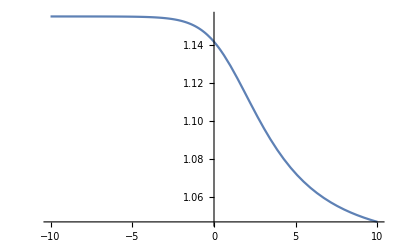

1.09697

{{-10.,1.1547},{-9.9,1.1547},{-9.8,1.1547},{-9.7,1.1547},{-9.6,1.1547},{-9.5,1.1547},{-9.4,1.1547},{-9.3,1.1547},{-9.2,1.1547},{-9.1,1.1547},{-9.,1.1547},{-8.9,1.1547},{-8.8,1.1547},{-8.7,1.1547},{-8.6,1.1547},{-8.5,1.1547},{-8.4,1.1547},{-8.3,1.1547},{-8.2,1.1547},{-8.1,1.1547},{-8.,1.15469},{-7.9,1.15469},{-7.8,1.15469},{-7.7,1.15469},{-7.6,1.15469},{-7.5,1.15469},{-7.4,1.15469},{-7.3,1.15469},{-7.2,1.15469},{-7.1,1.15469},{-7.,1.15468},{-6.9,1.15468},{-6.8,1.15468},{-6.7,1.15468},{-6.6,1.15468},{-6.5,1.15467},{-6.4,1.15467},{-6.3,1.15467},{-6.2,1.15466},{-6.1,1.15466},{-6.,1.15466},{-5.9,1.15465},{-5.8,1.15465},{-5.7,1.15464},{-5.6,1.15463},{-5.5,1.15463},{-5.4,1.15462},{-5.3,1.15461},{-5.2,1.1546},{-5.1,1.15459},{-5.,1.15458},{-4.9,1.15457},{-4.8,1.15455},{-4.7,1.15454},{-4.6,1.15452},{-4.5,1.1545},{-4.4,1.15448},{-4.3,1.15446},{-4.2,1.15443},{-4.1,1.1544},{-4.,1.15437},{-3.9,1.15434},{-3.8,1.1543},{-3.7,1.15426},{-3.6,1.15421},{-3.5,1.15416},{-3.4,1.15411},{-3.3,1.15404},{-3.2,1.15398},{-3.1,1.1539},{-3.,1.15382},{-2.9,1.15373},{-2.8,1.15363},{-2.7,1.15352},{-2.6,1.1534},{-2.5,1.15327},{-2.4,1.15312},{-2.3,1.15296},{-2.2,1.15278},{-2.1,1.15259},{-2.,1.15238},{-1.9,1.15215},{-1.8,1.1519},{-1.7,1.15162},{-1.6,1.15132},{-1.5,1.15099},{-1.4,1.15064},{-1.3,1.15025},{-1.2,1.14983},{-1.1,1.14937},{-1.,1.14888},{-0.9,1.14834},{-0.8,1.14777},{-0.7,1.14715},{-0.6,1.14648},{-0.5,1.14577},{-0.4,1.14501},{-0.3,1.1442},{-0.2,1.14334},{-0.1,1.14242},{0.,1.14145},{0.1,1.14043},{0.2,1.13935},{0.3,1.13822},{0.4,1.13704},{0.5,1.13581},{0.6,1.13453},{0.7,1.1332},{0.8,1.13182},{0.9,1.13041},{1.,1.12895},{1.1,1.12746},{1.2,1.12593},{1.3,1.12438},{1.4,1.1228},{1.5,1.12119},{1.6,1.11957},{1.7,1.11794},{1.8,1.11629},{1.9,1.11464},{2.,1.11299},{2.1,1.11133},{2.2,1.10969},{2.3,1.10804},{2.4,1.10641},{2.5,1.10479},{2.6,1.10319},{2.7,1.1016},{2.8,1.10003},{2.9,1.09849},{3.,1.09697},{3.1,1.09547},{3.2,1.094},{3.3,1.09255},{3.4,1.09114},{3.5,1.08975},{3.6,1.08839},{3.7,1.08706},{3.8,1.08576},{3.9,1.08449},{4.,1.08325},{4.1,1.08204},{4.2,1.08086},{4.3,1.07971},{4.4,1.07859},{4.5,1.0775},{4.6,1.07644},{4.7,1.07541},{4.8,1.0744},{4.9,1.07342},{5.,1.07247},{5.1,1.07154},{5.2,1.07064},{5.3,1.06977},{5.4,1.06892},{5.5,1.06809},{5.6,1.06729},{5.7,1.0665},{5.8,1.06575},{5.9,1.06501},{6.,1.06429},{6.1,1.06359},{6.2,1.06292},{6.3,1.06226},{6.4,1.06162},{6.5,1.06099},{6.6,1.06039},{6.7,1.0598},{6.8,1.05923},{6.9,1.05868},{7.,1.05814},{7.1,1.05761},{7.2,1.0571},{7.3,1.0566},{7.4,1.05612},{7.5,1.05565},{7.6,1.05519},{7.7,1.05475},{7.8,1.05431},{7.9,1.05389},{8.,1.05348},{8.1,1.05308},{8.2,1.05269},{8.3,1.05231},{8.4,1.05195},{8.5,1.05159},{8.6,1.05124},{8.7,1.05089},{8.8,1.05056},{8.9,1.05024},{9.,1.04992},{9.1,1.04961},{9.2,1.04931},{9.3,1.04902},{9.4,1.04874},{9.5,1.04846},{9.6,1.04819},{9.7,1.04792},{9.8,1.04766},{9.9,1.04741},{10.,1.04716}}

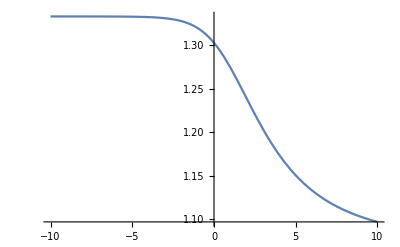

{{-10.,1.33333},{-9.9,1.33333},{-9.8,1.33333},{-9.7,1.33333},{-9.6,1.33333},{-9.5,1.33333},{-9.4,1.33333},{-9.3,1.33333},{-9.2,1.33333},{-9.1,1.33333},{-9.,1.33333},{-8.9,1.33333},{-8.8,1.33333},{-8.7,1.33333},{-8.6,1.33333},{-8.5,1.33332},{-8.4,1.33332},{-8.3,1.33332},{-8.2,1.33332},{-8.1,1.33332},{-8.,1.33332},{-7.9,1.33332},{-7.8,1.33332},{-7.7,1.33331},{-7.6,1.33331},{-7.5,1.33331},{-7.4,1.33331},{-7.3,1.33331},{-7.2,1.3333},{-7.1,1.3333},{-7.,1.3333},{-6.9,1.33329},{-6.8,1.33329},{-6.7,1.33328},{-6.6,1.33328},{-6.5,1.33327},{-6.4,1.33326},{-6.3,1.33326},{-6.2,1.33325},{-6.1,1.33324},{-6.,1.33323},{-5.9,1.33322},{-5.8,1.33321},{-5.7,1.33319},{-5.6,1.33318},{-5.5,1.33316},{-5.4,1.33315},{-5.3,1.33313},{-5.2,1.3331},{-5.1,1.33308},{-5.,1.33305},{-4.9,1.33302},{-4.8,1.33299},{-4.7,1.33296},{-4.6,1.33292},{-4.5,1.33287},{-4.4,1.33282},{-4.3,1.33277},{-4.2,1.33271},{-4.1,1.33265},{-4.,1.33258},{-3.9,1.3325},{-3.8,1.33241},{-3.7,1.33231},{-3.6,1.33221},{-3.5,1.33209},{-3.4,1.33196},{-3.3,1.33182},{-3.2,1.33166},{-3.1,1.33149},{-3.,1.3313},{-2.9,1.33109},{-2.8,1.33086},{-2.7,1.33061},{-2.6,1.33033},{-2.5,1.33002},{-2.4,1.32969},{-2.3,1.32932},{-2.2,1.32891},{-2.1,1.32847},{-2.,1.32798},{-1.9,1.32745},{-1.8,1.32687},{-1.7,1.32623},{-1.6,1.32554},{-1.5,1.32479},{-1.4,1.32396},{-1.3,1.32307},{-1.2,1.3221},{-1.1,1.32105},{-1.,1.31992},{-0.9,1.31869},{-0.8,1.31737},{-0.7,1.31595},{-0.6,1.31443},{-0.5,1.31279},{-0.4,1.31105},{-0.3,1.30919},{-0.2,1.30722},{-0.1,1.30512},{0.,1.30291},{0.1,1.30058},{0.2,1.29812},{0.3,1.29555},{0.4,1.29286},{0.5,1.29006},{0.6,1.28715},{0.7,1.28414},{0.8,1.28103},{0.9,1.27782},{1.,1.27453},{1.1,1.27116},{1.2,1.26772},{1.3,1.26422},{1.4,1.26067},{1.5,1.25708},{1.6,1.25344},{1.7,1.24979},{1.8,1.24611},{1.9,1.24243},{2.,1.23874},{2.1,1.23506},{2.2,1.2314},{2.3,1.22776},{2.4,1.22414},{2.5,1.22056},{2.6,1.21702},{2.7,1.21352},{2.8,1.21007},{2.9,1.20667},{3.,1.20333},{3.1,1.20005},{3.2,1.19683},{3.3,1.19367},{3.4,1.19058},{3.5,1.18755},{3.6,1.18459},{3.7,1.1817},{3.8,1.17888},{3.9,1.17612},{4.,1.17344},{4.1,1.17082},{4.2,1.16827},{4.3,1.16578},{4.4,1.16337},{4.5,1.16101},{4.6,1.15873},{4.7,1.1565},{4.8,1.15434},{4.9,1.15224},{5.,1.15019},{5.1,1.14821},{5.2,1.14628},{5.3,1.1444},{5.4,1.14258},{5.5,1.14082},{5.6,1.1391},{5.7,1.13743},{5.8,1.13581},{5.9,1.13424},{6.,1.13271},{6.1,1.13123},{6.2,1.12979},{6.3,1.12839},{6.4,1.12703},{6.5,1.12571},{6.6,1.12443},{6.7,1.12318},{6.8,1.12197},{6.9,1.12079},{7.,1.11965},{7.1,1.11854},{7.2,1.11746},{7.3,1.11641},{7.4,1.11539},{7.5,1.1144},{7.6,1.11343},{7.7,1.11249},{7.8,1.11158},{7.9,1.11069},{8.,1.10982},{8.1,1.10898},{8.2,1.10816},{8.3,1.10736},{8.4,1.10659},{8.5,1.10583},{8.6,1.1051},{8.7,1.10438},{8.8,1.10368},{8.9,1.103},{9.,1.10234},{9.1,1.10169},{9.2,1.10106},{9.3,1.10045},{9.4,1.09985},{9.5,1.09926},{9.6,1.09869},{9.7,1.09814},{9.8,1.09759},{9.9,1.09706},{10.,1.09655}}

```mathematica
F[k_,η_] := NIntegrate[x^k/(Exp[x-η]+1),{x,0,∞}];
F[2,3]/F[3,3]
Plot[(F[4,η]/F[2,η])^(1/2)/(F[3,η]/F[2,η]),{η,-10,10}]
(F[4,3]/F[2,3])^(1/2)/(F[3,3]/F[2,3])
Table[{η,(F[4,η]/F[2,η])^(1/2)/(F[3,η]/F[2,η])},{η,-10,10,0.1}]
Plot[(F[4,η]/F[3,η])(F[2,η]/F[3,η]),{η,-10,10}]
Table[{η,(F[4,η]/F[3,η])(F[2,η]/F[3,η])},{η,-10,10,0.1}]
```